```mathematica
input3=Import["Z:\\Antara\\Data analysis\\2021-06-17\\new analysis\\cutoff determination\\35-mGold step ratio.xlsx",{"Data",1}];
input4=Import["Z:\\Antara\\Data analysis\\2021-06-17\\new analysis\\cutoff determination\\44-mEGFP step ratio.xlsx",{"Data",1}];
list1=input3⟦All,1⟧;
list2=input4⟦All,1⟧;

sum=Table[
a= Length[Select[list1,#>cutoff&]]/Length[list1];
b= Length[Select[list2,#<cutoff&]]/Length[list2];
{cutoff,N[a+b]}
,{cutoff,0.5,1.8,0.01}]
```

{{0.5,0.246328},{0.51,0.246328},{0.52,0.234183},{0.53,0.217988},{0.54,0.205843},{0.55,0.197745},{0.56,0.193697},{0.57,0.181551},{0.58,0.173454},{0.59,0.175941},{0.6,0.171893},{0.61,0.163796},{0.62,0.159747},{0.63,0.147601},{0.64,0.143553},{0.65,0.143553},{0.66,0.139504},{0.67,0.139504},{0.68,0.131407},{0.69,0.131407},{0.7,0.12331},{0.71,0.115213},{0.72,0.115213},{0.73,0.120187},{0.74,0.116139},{0.75,0.11209},{0.76,0.11209},{0.77,0.11209},{0.78,0.11209},{0.79,0.11209},{0.8,0.118626},{0.81,0.125162},{0.82,0.127649},{0.83,0.127649},{0.84,0.127649},{0.85,0.123601},{0.86,0.123601},{0.87,0.123601},{0.88,0.123601},{0.89,0.123601},{0.9,0.119552},{0.91,0.119552},{0.92,0.119552},{0.93,0.126088},{0.94,0.126088},{0.95,0.117991},{0.96,0.109894},{0.97,0.109894},{0.98,0.109894},{0.99,0.105845},{1.,0.105845},{1.01,0.105845},{1.02,0.105845},{1.03,0.105845},{1.04,0.101797},{1.05,0.0977481},{1.06,0.0977481},{1.07,0.0977481},{1.08,0.0977481},{1.09,0.0977481},{1.1,0.0977481},{1.11,0.0977481},{1.12,0.0977481},{1.13,0.0977481},{1.14,0.0977481},{1.15,0.104284},{1.16,0.104284},{1.17,0.11082},{1.18,0.117356},{1.19,0.117356},{1.2,0.117356},{1.21,0.117356},{1.22,0.117356},{1.23,0.117356},{1.24,0.117356},{1.25,0.113307},{1.26,0.119843},{1.27,0.119843},{1.28,0.119843},{1.29,0.126379},{1.3,0.126379},{1.31,0.126379},{1.32,0.132915},{1.33,0.139451},{1.34,0.139451},{1.35,0.139451},{1.36,0.145987},{1.37,0.145987},{1.38,0.165595},{1.39,0.165595},{1.4,0.165595},{1.41,0.165595},{1.42,0.178667},{1.43,0.191739},{1.44,0.200762},{1.45,0.226906},{1.46,0.246514},{1.47,0.266122},{1.48,0.279193},{1.49,0.281681},{1.5,0.281681},{1.51,0.294753},{1.52,0.301289},{1.53,0.314361},{1.54,0.327432},{1.55,0.340504},{1.56,0.366648},{1.57,0.373184},{1.58,0.399328},{1.59,0.4124},{1.6,0.425472},{1.61,0.432008},{1.62,0.454103},{1.63,0.486783},{1.64,0.493319},{1.65,0.502342},{1.66,0.515414},{1.67,0.548093},{1.68,0.567701},{1.69,0.570189},{1.7,0.576725},{1.71,0.583261},{1.72,0.583261},{1.73,0.602868},{1.74,0.609404},{1.75,0.629012},{1.76,0.629012},{1.77,0.642084},{1.78,0.655156},{1.79,0.655156},{1.8,0.655156}}

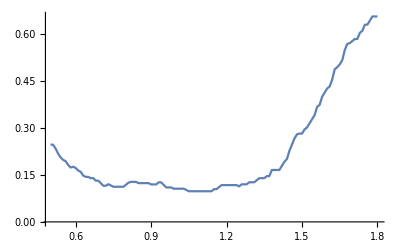

```mathematica
ListPlot[sum,Joined->True]
```

```mathematica
sum⟦Position[sum,_?(#⟦2⟧==Min[sum⟦All,2⟧]&)]//Flatten⟧//Quiet
```

{{1.05,0.0977481},{1.06,0.0977481},{1.07,0.0977481},{1.08,0.0977481},{1.09,0.0977481},{1.1,0.0977481},{1.11,0.0977481},{1.12,0.0977481},{1.13,0.0977481},{1.14,0.0977481}}